```mathematica
Infinite TEBD code for the quantum Ising model,
Recover the FIG5 and FIG6 of Vidal's original work: cond-mat/0605597
```

Initialization of Notebook

```mathematica
ClearAll["Global`*"];ClearSystemCache[];
σx={{0,1.},{1.,0}};σz={{1.,0},{0,-1.}};σi={{1.,0},{0,1.}};
```

Tensor Functions

```mathematica
initializeTensors[dim_,bond_]:=Module[{swap,norm,contract,U,S,V},
LB=DiagonalMatrix[ReverseSort@Table[RandomReal[],bond]];LB=LB/Sqrt[Tr[LB.LB]];
swap=Table[RandomReal[],dim,bond,dim,bond];
contract={{1,5},{2,6},{3,7},{4,8}};
norm=Activate@TensorContract[Inactive[TensorProduct][Conjugate@swap,swap],contract];
swap=swap/Sqrt[norm];
swap=ArrayReshape[swap,{dim*bond,dim*bond}];
{U,S,V}=SingularValueDecomposition[swap,bond];LA=S/Sqrt[Tr[S.S]];
GA=Activate@TensorContract[Inactive[TensorProduct][PseudoInverse@LB,ArrayReshape[U,{dim,bond,bond}]],{2,4}]//Transpose;
GB=Activate@TensorContract[Inactive[TensorProduct][ArrayReshape[V†,{bond,dim,bond}],PseudoInverse@LB],{3,4}]//Transpose;];

GSA[]:=Module[{R,L,psi},
R=Activate@TensorContract[Inactive[TensorProduct][GB,LB],{3,4}];
R=Activate@TensorContract[Inactive[TensorProduct][LA,R],{2,4}];
L=Activate@TensorContract[Inactive[TensorProduct][LB,GA],{2,4}];
psi=Activate@TensorContract[Inactive[TensorProduct][L,R],{3,4}]//Transpose//Return;];

GSB[]:=Module[{R,L,psi},
R=Activate@TensorContract[Inactive[TensorProduct][GA,LA],{3,4}];
R=Activate@TensorContract[Inactive[TensorProduct][LB,R],{2,4}];
L=Activate@TensorContract[Inactive[TensorProduct][LA,GB],{2,4}];
psi=Activate@TensorContract[Inactive[TensorProduct][L,R],{3,4}]//Transpose//Return;];

upDateA[switch_]/;switch==1||switch==2:=Module[{psi,gate,U,S,V},
If[switch==1,gate=RU,gate=IU];
psi=Transpose[Activate@TensorContract[Inactive[TensorProduct][gate,GSA[]],{{3,5},{4,7}}],{1,3,2,4}];
psi=ArrayReshape[psi,{dim*bond,dim*bond}];
{U,S,V}=SingularValueDecomposition[psi,bond];LA=S/Sqrt[Tr[S.S]];
GA=Activate@TensorContract[Inactive[TensorProduct][PseudoInverse@LB,ArrayReshape[U,{dim,bond,bond}]],{2,4}]//Transpose;
GB=Activate@TensorContract[Inactive[TensorProduct][ArrayReshape[V†,{bond,dim,bond}],PseudoInverse@LB],{3,4}]//Transpose;];

upDateB[switch_]/;switch==1||switch==2:=Module[{psi,gate,U,S,V},
If[switch==1,gate=RU,gate=IU];
psi=Transpose[Activate@TensorContract[Inactive[TensorProduct][gate,GSB[]],{{3,5},{4,7}}],{1,3,2,4}];
psi=ArrayReshape[psi,{dim*bond,dim*bond}];
{U,S,V}=SingularValueDecomposition[psi,bond];LB=S/Sqrt[Tr[S.S]];
GB=Activate@TensorContract[Inactive[TensorProduct][PseudoInverse@LA,ArrayReshape[U,{dim,bond,bond}]],{2,4}]//Transpose;
GA=Activate@TensorContract[Inactive[TensorProduct][ArrayReshape[V†,{bond,dim,bond}],PseudoInverse@LA],{3,4}]//Transpose;];

gateU[switch_,time_,ham_]/;switch==1||switch==2:=
If[switch==1,ArrayReshape[MatrixExp[-I time ham],Table[dim,4]]//Return,ArrayReshape[MatrixExp[-time ham],Table[dim,4]]//Return;];
```

Measure Functions

```mathematica
mA[op_]:=Module[{psi,result},
psi=Activate@TensorContract[Inactive[TensorProduct][GA,LA],{3,4}];
psi=Activate@TensorContract[Inactive[TensorProduct][LB,psi],{2,4}]//Transpose;
result=Activate@TensorContract[Inactive[TensorProduct][Conjugate@psi,psi],{{2,5},{3,6}}];
result=Tr[result.op]//Return;];

mB[op_]:=Module[{psi,result},
psi=Activate@TensorContract[Inactive[TensorProduct][GB,LB],{3,4}];
psi=Activate@TensorContract[Inactive[TensorProduct][LA,psi],{2,4}]//Transpose;
result=Activate@TensorContract[Inactive[TensorProduct][Conjugate@psi,psi],{{2,5},{3,6}}];
result=Tr[result.op]//Return;];

twoC[op1_,op2_,distance_]:=Module[{psi,swap,alt,A1,A2,B2,store={},count},
psi=Activate@TensorContract[Inactive[TensorProduct][GA,LA],{3,4}];
psi=Activate@TensorContract[Inactive[TensorProduct][LB,psi],{2,4}]//Transpose;
swap=Activate@TensorContract[Inactive[TensorProduct][op1,psi],{2,3}];
A1=Activate@TensorContract[Inactive[TensorProduct][Conjugate@psi,swap],{{1,4},{2,5}}];
psi=Activate@TensorContract[Inactive[TensorProduct][GA,LA],{3,4}];
swap=Activate@TensorContract[Inactive[TensorProduct][op2,psi],{2,3}];
A2=Activate@TensorContract[Inactive[TensorProduct][Conjugate@psi,swap],{{1,4},{3,6}}];
psi=Activate@TensorContract[Inactive[TensorProduct][GB,LB],{3,4}];
swap=Activate@TensorContract[Inactive[TensorProduct][op2,psi],{2,3}];
B2=Activate@TensorContract[Inactive[TensorProduct][Conjugate@psi,swap],{{1,4},{3,6}}];
Do[
If[Mod[count,2]==1,
swap=Activate@TensorContract[Inactive[TensorProduct][GB,LB],{3,4}];
alt=Activate@TensorContract[Inactive[TensorProduct][A1,swap],{2,4}];
alt=Activate@TensorContract[Inactive[TensorProduct][Conjugate@swap,alt],{{1,5},{2,4}}];
swap=Activate@TensorContract[Inactive[TensorProduct][A1,B2],{{1,3},{2,4}}],
swap=Activate@TensorContract[Inactive[TensorProduct][GA,LA],{3,4}];
alt=Activate@TensorContract[Inactive[TensorProduct][A1,swap],{2,4}];
alt=Activate@TensorContract[Inactive[TensorProduct][Conjugate@swap,alt],{{1,5},{2,4}}];
swap=Activate@TensorContract[Inactive[TensorProduct][A1,A2],{{1,3},{2,4}}];];
AppendTo[store,{count,Abs[swap-4 m^2]}];A1=alt;If[Mod[count,50]==0,Print@count];
,{count,1,distance}];
Return@store;];
```

GS Finding & Time Simulating Function

```mathematica
findGS[hz_,digit_,loop_]:=
(Do[IU=gateU[2,Power[10,-iter],H[hz]];
Do[upDateA[2];upDateB[2];m=(mA[σz]+mB[σz])/4//Abs;
,loop];Print[iter];
,{iter,0,digit}];)

enTime[hz_,δt_,ttime_]:=
(RU=gateU[1,δt/2,H[hz]];
Do[upDateA[1];upDateB[1];upDateB[1];upDateA[1];
AppendTo[mz,{time=step δt,(mA[σz]+mB[σz])/4//Abs}];Print[time];
,{step,1,Ceiling[ttime/δt]}];)
```

Main Function

```mathematica
dim=2;bond=10;δt=0.01;T=1;mz={};
H[hz_]:=KroneckerProduct[σx,σx]+hz/2 (KroneckerProduct[σz,σi]+KroneckerProduct[σi,σz]);
initializeTensors[dim,bond];
m=(mA[σz]+mB[σz])/4//Abs;
(* find GS *)
findGS[10,5,20];Print["GS is Found!"];
(* calculate two point correlation *)
cor=twoC[σz,σz,100];Print["Correlation Function Calulation Is Done!"]
(* simulation with time *)
AppendTo[mz,{0,m}];
enTime[3,δt,T];Print["Finished!"];
```

```mathematica
ListLinePlot[mz,Frame->True,PlotRange->All,PlotStyle->{Black},PlotRange->{All,{0.475,0.498}}]
ListLogLogPlot[cor,Frame->True,PlotRange->All,PlotStyle->Black]
```

FIG. 5&6 Show

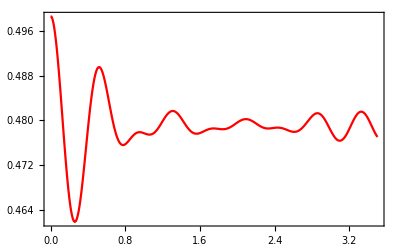
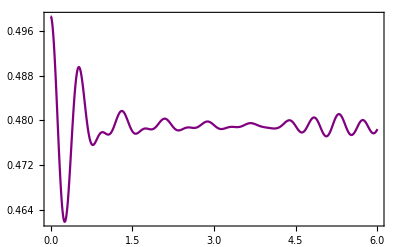
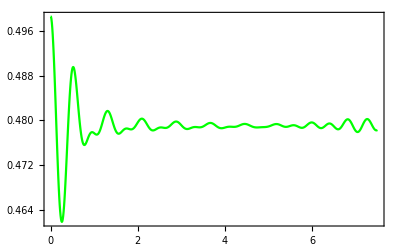
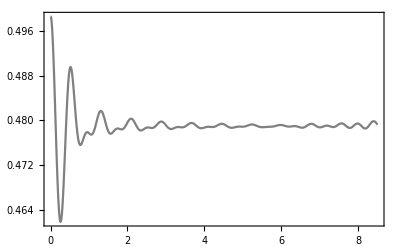
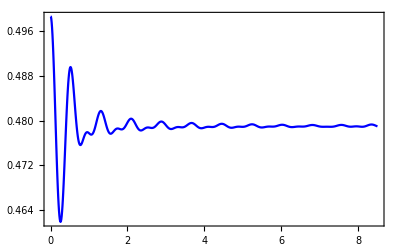
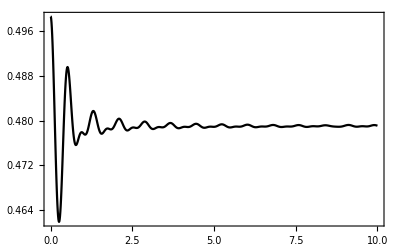
```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange->{All,{0.475,0.498}}]
```

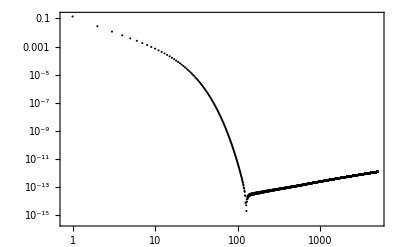
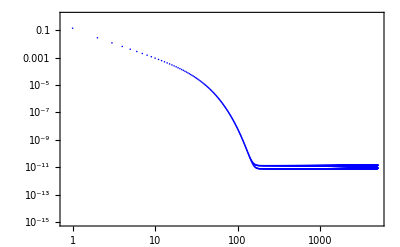
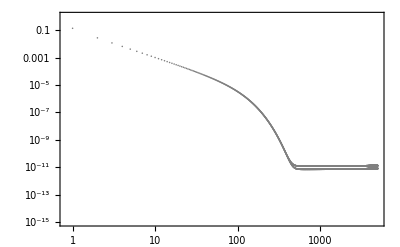
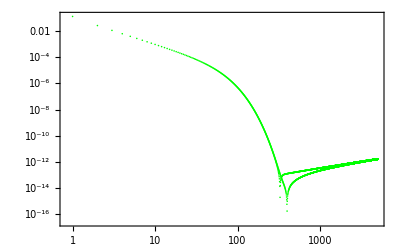
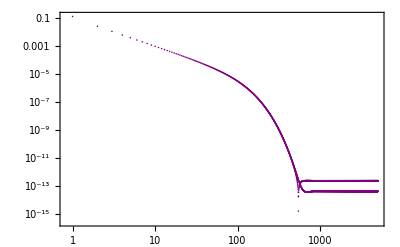
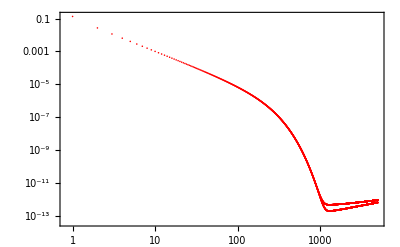
```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},PlotRange->All]
```